# QKT

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Breaking time reversal symmetry\\QKT.wl"];
```

```mathematica
LaunchKernels[14];
```

# Parity separation

```mathematica
Print["Computing Floquet matrix..."];
J=1001/2;
α=Pi/2.;
k=10.;
Clear[mat];
mat=Floq[J,α,k];
d=2 J+1;
```

Computing Floquet matrix...

```mathematica
(*1. Fast,Universal Parity Sector Separation*)
(*Sx^2 strictly couples m to m±2,meaning alternating array indices ALWAYS decouple.*)
If[IntegerQ[J]&&OddQ[J],
(*If J is an odd integer,the highest m (index 1) is odd.Thus,index 2 starts the Even m sector.*)idxEvenM=Range[2,d,2];
idxOddM=Range[1,d,2];,
(*If J is an even integer,the highest m (index 1) is even.*)(*If J is a half-integer,'Even/Odd' m doesn't exist,so we default to standard decoupling.*)idxEvenM=Range[1,d,2];
idxOddM=Range[2,d,2];];
```

```mathematica
(*2. Extract the submatrices based on the physical indices*)
matEven=mat[[idxEvenM,idxEvenM]];
matOdd=mat[[idxOddM,idxOddM]];
```

```mathematica
(*3. Diagonalize both sectors*)
{eigenvalEven,eigenvecEven}=Eigensystem[matEven,Method->"Direct"];
{eigenvalOdd,eigenvecOdd}=Eigensystem[matOdd,Method->"Direct"];
```

```mathematica
(*4. Reconstruct full eigenvectors robustly*)
neweigenvecEven=Table[vec=ConstantArray[0.,d];
vec[[idxEvenM]]=eigenvecEven[[j]];
vec,{j,Length[idxEvenM]}];

neweigenvecOdd=Table[vec=ConstantArray[0.,d];
vec[[idxOddM]]=eigenvecOdd[[j]];
vec,{j,Length[idxOddM]}];
```

```mathematica
(*5. Combine the final spectrum*)
neweigenvec=Join[neweigenvecEven,neweigenvecOdd];
neweigenval=Join[eigenvalEven,eigenvalOdd];
```

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalEven]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalOdd]]]}
```

{0.514199,0.51472}

```mathematica
phases=Sort[Arg[eigenvalEven]];
phases=Sort[Arg[eigenvalOdd]];
data=Table[{phases[[i]],i},{i,1,Length[phases]}];
```

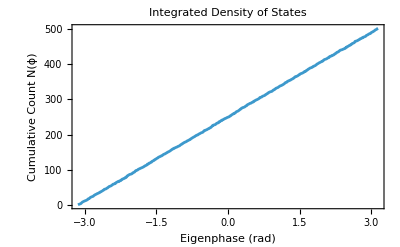

```mathematica
(*3. Plot the staircase function*)
ListPlot[data,Frame->True,FrameLabel->{"Eigenphase (rad)","Cumulative Count N(ϕ)"},PlotLabel->"Integrated Density of States",Joined->True]
```

```mathematica
n=Length[phases];
unfolded=phases*(n/(2*Pi));
spacings=Differences[unfolded];
meanSpacing=Mean[spacings];
spacings=spacings/meanSpacing;
```

```mathematica
poisson[s_]:=Exp[-s];
wignerDyson[s_]:=(Pi*s/2)*Exp[-(Pi*s^2)/4];
```

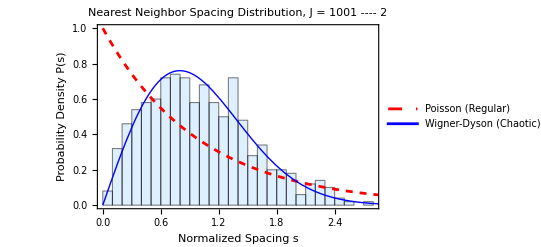

```mathematica
Show[Histogram[spacings,{0.1},"PDF",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Normalized Spacing s","Probability Density P(s)"},PlotLabel->"Nearest Neighbor Spacing Distribution, J = "<>ToString[J]],Plot[{poisson[s],wignerDyson[s]},{s,0,4},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","Wigner-Dyson (Chaotic)"}]]
```